```mathematica
f[x_,y_]:=KroneckerDelta[x,y]
```

```mathematica
xx={{f[l,p],f[l,m],f[l,n]},{f[m,p],f[m,m],f[m,n]},{f[n,p],f[n,m],f[n,n]}}
```

{{KroneckerDelta[l,p],KroneckerDelta[l,m],KroneckerDelta[l,n]},{KroneckerDelta[m,p],1,KroneckerDelta[m,n]},{KroneckerDelta[n,p],KroneckerDelta[m,n],1}}

```mathematica
Det[xx]
```

KroneckerDelta[l,p]-KroneckerDelta[l,p] KroneckerDelta[m,n]^2-KroneckerDelta[l,m] KroneckerDelta[m,p]+KroneckerDelta[l,n] KroneckerDelta[m,n] KroneckerDelta[m,p]-KroneckerDelta[l,n] KroneckerDelta[n,p]+KroneckerDelta[l,m] KroneckerDelta[m,n] KroneckerDelta[n,p]

```mathematica
Det[{{lp,lm,ln},{mp,mm,mn},{np,nm,nn}}]
```

-lp mn nm+ln mp nm+lp mm nn-lm mp nn-ln mm np+lm mn np

```mathematica
yy={{f[k,p],f[k,w],f[k,m],f[k,n]},{f[l,p],f[l,w],f[l,m],f[l,n]},{f[m,p],f[m,w],f[m,m],f[m,n]},{f[n,p],f[n,w],f[n,m],f[n,n]}}
```

{{KroneckerDelta[k,p],KroneckerDelta[k,w],KroneckerDelta[k,m],KroneckerDelta[k,n]},{KroneckerDelta[l,p],KroneckerDelta[l,w],KroneckerDelta[l,m],KroneckerDelta[l,n]},{KroneckerDelta[m,p],KroneckerDelta[m,w],1,KroneckerDelta[m,n]},{KroneckerDelta[n,p],KroneckerDelta[n,w],KroneckerDelta[m,n],1}}

```mathematica
Det[yy]
```

-KroneckerDelta[k,w] KroneckerDelta[l,p]+KroneckerDelta[k,p] KroneckerDelta[l,w]+KroneckerDelta[k,w] KroneckerDelta[l,p] KroneckerDelta[m,n]^2-KroneckerDelta[k,p] KroneckerDelta[l,w] KroneckerDelta[m,n]^2+KroneckerDelta[k,w] KroneckerDelta[l,m] KroneckerDelta[m,p]-KroneckerDelta[k,m] KroneckerDelta[l,w] KroneckerDelta[m,p]-KroneckerDelta[k,w] KroneckerDelta[l,n] KroneckerDelta[m,n] KroneckerDelta[m,p]+KroneckerDelta[k,n] KroneckerDelta[l,w] KroneckerDelta[m,n] KroneckerDelta[m,p]-KroneckerDelta[k,p] KroneckerDelta[l,m] KroneckerDelta[m,w]+KroneckerDelta[k,m] KroneckerDelta[l,p] KroneckerDelta[m,w]+KroneckerDelta[k,p] KroneckerDelta[l,n] KroneckerDelta[m,n] KroneckerDelta[m,w]-KroneckerDelta[k,n] KroneckerDelta[l,p] KroneckerDelta[m,n] KroneckerDelta[m,w]+KroneckerDelta[k,w] KroneckerDelta[l,n] KroneckerDelta[n,p]-KroneckerDelta[k,n] KroneckerDelta[l,w] KroneckerDelta[n,p]-KroneckerDelta[k,w] KroneckerDelta[l,m] KroneckerDelta[m,n] KroneckerDelta[n,p]+KroneckerDelta[k,m] KroneckerDelta[l,w] KroneckerDelta[m,n] KroneckerDelta[n,p]+KroneckerDelta[k,n] KroneckerDelta[l,m] KroneckerDelta[m,w] KroneckerDelta[n,p]-KroneckerDelta[k,m] KroneckerDelta[l,n] KroneckerDelta[m,w] KroneckerDelta[n,p]-KroneckerDelta[k,p] KroneckerDelta[l,n] KroneckerDelta[n,w]+KroneckerDelta[k,n] KroneckerDelta[l,p] KroneckerDelta[n,w]+KroneckerDelta[k,p] KroneckerDelta[l,m] KroneckerDelta[m,n] KroneckerDelta[n,w]-KroneckerDelta[k,m] KroneckerDelta[l,p] KroneckerDelta[m,n] KroneckerDelta[n,w]-KroneckerDelta[k,n] KroneckerDelta[l,m] KroneckerDelta[m,p] KroneckerDelta[n,w]+KroneckerDelta[k,m] KroneckerDelta[l,n] KroneckerDelta[m,p] KroneckerDelta[n,w]

```mathematica
yy1={{kp,kw,km,kn},{lp,lw,lm,ln},{mp,mw,mm,mn},{np,nw,nm,nn}}
```

{{kp,kw,km,kn},{lp,lw,lm,ln},{mp,mw,mm,mn},{np,nw,nm,nn}}

```mathematica
Det[yy1]
```

kw lp mn nm-kp lw mn nm-kw ln mp nm+kn lw mp nm+kp ln mw nm-kn lp mw nm-kw lp mm nn+kp lw mm nn+kw lm mp nn-km lw mp nn-kp lm mw nn+km lp mw nn+kw ln mm np-kn lw mm np-kw lm mn np+km lw mn np+kn lm mw np-km ln mw np-kp ln mm nw+kn lp mm nw+kp lm mn nw-km lp mn nw-kn lm mp nw+km ln mp nw

```mathematica
∮_closed
```

```mathematica
\underset{\text{closed}}{\oint}
```

```mathematica
test1={{kp,kl,km,kn},{lp,ll,lm,ln},{mp,ml,mm,mn},{np,nl,nm,nn}}
%//MatrixForm
```

{{kp,kl,km,kn},{lp,ll,lm,ln},{mp,ml,mm,mn},{np,nl,nm,nn}}

(kp | kl | km | kn
lp | ll | lm | ln
mp | ml | mm | mn
np | nl | nm | nn)

```mathematica
Det[test1]
```

-kp ln mm nl+kn lp mm nl+kp lm mn nl-km lp mn nl-kn lm mp nl+km ln mp nl+kp ln ml nm-kn lp ml nm-kp ll mn nm+kl lp mn nm+kn ll mp nm-kl ln mp nm-kp lm ml nn+km lp ml nn+kp ll mm nn-kl lp mm nn-km ll mp nn+kl lm mp nn+kn lm ml np-km ln ml np-kn ll mm np+kl ln mm np+km ll mn np-kl lm mn np

```mathematica
Block[{d=3},d^3-6 d^2+11d-6]
```

0

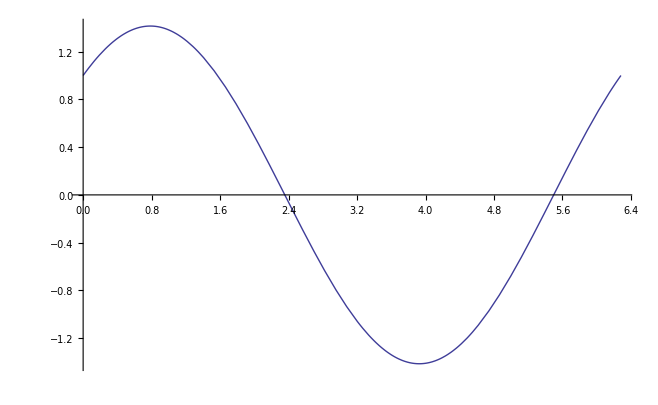

```mathematica
Plot[Cos[x]+Sin[x],{x,0,2Pi}]
```

Quit kernel to calculate the following.

ˆ r = sinθcosφ ˆ x + sinθsinφ ˆ y + cosθ ˆ z
ˆθ = cosθcosφ ˆ x + cosθsinφ ˆ y − sinθ ˆ z
ˆφ = −sinφ ˆ x + cosφ ˆ y.

```mathematica
sol=Solve[rr==Sin[θ] Cos[ϕ] xx + Sin[θ]Sin[ϕ] yy + Cos[θ]zz &&θθ==Cos[θ]Cos[ϕ]xx+Cos[θ]Sin[ϕ]yy-Sin[θ]zz&&ϕϕ==-Sin[ϕ]xx+Cos[ϕ]yy,{xx,yy,zz}]//Simplify
```

{{xx→θθ Cos[θ] Cos[ϕ]+rr Cos[ϕ] Sin[θ]-ϕϕ Sin[ϕ],yy→ϕϕ Cos[ϕ]+(θθ Cos[θ]+rr Sin[θ]) Sin[ϕ],zz→rr Cos[θ]-θθ Sin[θ]}}

```mathematica
D[Sin[θ] Cos[ϕ] xx + Sin[θ]Sin[ϕ] yy + Cos[θ]zz,θ]/.sol
%//Simplify
```

{-Sin[θ] (rr Cos[θ]-θθ Sin[θ])+Cos[θ] Cos[ϕ] (θθ Cos[θ] Cos[ϕ]+rr Cos[ϕ] Sin[θ]-ϕϕ Sin[ϕ])+Cos[θ] Sin[ϕ] (ϕϕ Cos[ϕ]+(θθ Cos[θ]+rr Sin[θ]) Sin[ϕ])}

{θθ}

```mathematica
D[Sin[θ] Cos[ϕ] xx + Sin[θ]Sin[ϕ] yy + Cos[θ]zz,ϕ]/.sol
%//Simplify
```

{-Sin[θ] Sin[ϕ] (θθ Cos[θ] Cos[ϕ]+rr Cos[ϕ] Sin[θ]-ϕϕ Sin[ϕ])+Cos[ϕ] Sin[θ] (ϕϕ Cos[ϕ]+(θθ Cos[θ]+rr Sin[θ]) Sin[ϕ])}

{ϕϕ Sin[θ]}

```mathematica
D[Cos[θ]Cos[ϕ]xx+Cos[θ]Sin[ϕ]yy-Sin[θ]zz,θ]/.sol
%//Simplify
```

{-Cos[θ] (rr Cos[θ]-θθ Sin[θ])-Cos[ϕ] Sin[θ] (θθ Cos[θ] Cos[ϕ]+rr Cos[ϕ] Sin[θ]-ϕϕ Sin[ϕ])-Sin[θ] Sin[ϕ] (ϕϕ Cos[ϕ]+(θθ Cos[θ]+rr Sin[θ]) Sin[ϕ])}

{-rr}

```mathematica
D[Cos[θ]Cos[ϕ]xx+Cos[θ]Sin[ϕ]yy-Sin[θ]zz,ϕ]/.sol
%//Simplify
```

{-Cos[θ] Sin[ϕ] (θθ Cos[θ] Cos[ϕ]+rr Cos[ϕ] Sin[θ]-ϕϕ Sin[ϕ])+Cos[θ] Cos[ϕ] (ϕϕ Cos[ϕ]+(θθ Cos[θ]+rr Sin[θ]) Sin[ϕ])}

{ϕϕ Cos[θ]}

```mathematica
D[-Sin[ϕ]xx+Cos[ϕ]yy,ϕ]/.sol
%//Simplify
```

{-Cos[ϕ] (θθ Cos[θ] Cos[ϕ]+rr Cos[ϕ] Sin[θ]-ϕϕ Sin[ϕ])-Sin[ϕ] (ϕϕ Cos[ϕ]+(θθ Cos[θ]+rr Sin[θ]) Sin[ϕ])}

{-θθ Cos[θ]-rr Sin[θ]}

```mathematica
gammaθ={{0,0},{0,(r Cos[θ])/(R + r Sin[θ])}}
%//MatrixForm
```

{{0,0},{0,(r Cos[θ])/(R+r Sin[θ])}}

(0 | 0
0 | (r Cos[θ])/(R+r Sin[θ]))

```mathematica
gammaϕ={{(r Cos[θ])/(R + r Sin[θ]),-Cos[θ](R+r Sin[θ])/r},{(r Cos[θ])/(R + r Sin[θ]),0}}
%//MatrixForm
```

{{(r Cos[θ])/(R+r Sin[θ]),-(Cos[θ] (R+r Sin[θ]))/r},{(r Cos[θ])/(R+r Sin[θ]),0}}

((r Cos[θ])/(R+r Sin[θ]) | -(Cos[θ] (R+r Sin[θ]))/r
(r Cos[θ])/(R+r Sin[θ]) | 0)

```mathematica
gammaθ . gammaϕ-gammaϕ . gammaθ
%//MatrixForm
```

{{0,Cos[θ]^2},{(r^2 Cos[θ]^2)/(R+r Sin[θ])^2,0}}

(0 | Cos[θ]^2
(r^2 Cos[θ]^2)/(R+r Sin[θ])^2 | 0)